```mathematica
SetOptions[EvaluationNotebook[],CellEpilog:>SelectionMove[EvaluationNotebook[],Next,Cell]]
```

Variables used in model

```mathematica
(* variables and parameters at (homogeneous) steady state *)
ssvars = { ξ-> 0.1, koff->0.1, kon-> 0.0001, Dμ->1, Dc-> 10, β->0.01, α->0.01 ,kd->  0.00001 ,kp->1000,K->0.2 (*kp/(2*kd*μ0)*),R-> 10, μ0->10000, Pe-> 5,ρ0->kp/(2*kd*μ0)+Sqrt[kp^2/(2*kd*μ0)^2 - K^2], ζ-> -Pe*ξ*(Dc*koff + Dμ*kon*ρ0)/(kon*ρ0*μ0)}; (*kon replaced by kon*ρ0 *)
n = 2;
startρ = ρ0//.ssvars;
(* for n=2,  kp/(2*kd*μ0)±Sqrt[kp^2/(2*kd*μ0)^2 - K^2]
for n=1, kp/kd/mu0 - K
for n=0, kp/kd/mu0/(K + 1) *)
startc = koff*μ0/(kon*startρ)//.ssvars;
startμ = μ0//.ssvars;
kappa=0.01;
Tend = 300;
```

solver for 1D cell

```mathematica
pdeSolve[rdvariables_] :=Module[{sol},
sol = NDSolve[{
D[ρ[θ, t], t]+(1/R)*D[(ρ[θ, t] *v[θ, t]), θ]==kp*ρ[θ, t]^n/(K^n+ρ[θ, t]^n)-kd*μ[θ, t]*ρ[θ, t],
D[(-ζ*μ[θ, t] -α*ρ[θ, t] + (β/R^2)*D[ρ[θ, t], θ,θ]), θ] ==ξ *R *v[θ, t],
D[c[θ, t], t]== (Dc/R^2)* D[c[θ, t], θ,θ]-kon*ρ[θ, t]*c[θ, t]+koff*μ[θ, t],
D[μ[θ, t], t]+(1/R)* D[(μ[θ, t]*v[θ, t]), θ]== kon*ρ[θ, t]*c[θ, t]-koff*μ[θ, t] + (Dμ/R^2)*D[μ[θ,t], θ,θ],

c[θ,0]==startc + kappa*Cos[θ] ,
μ[θ,0]==startμ  + kappa*Cos[θ],
ρ[θ,0]==startρ + kappa*Cos[θ],
v[θ,0]== kappa*(ζ+α+β/R^2)*Sin[θ] /ξ /R,

μ[-Pi, t]==μ[Pi, t],
c[-Pi, t]==c[Pi, t],
ρ[-Pi, t]==ρ[Pi, t],
v[-Pi,t]==v[Pi,t]}//.rdvariables,{μ, c, ρ, v},{θ,-Pi,Pi},{t, 0,Tend}, MaxStepFraction->1/200,Method->Automatic,AccuracyGoal->1,PrecisionGoal->5]; Return[sol]]
```

```mathematica
(* alternatively can try Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->nx,"MaxPoints"->nx},Method->{"IDA","ImplicitSolver"->{"GMRES"}}} *)
```

```mathematica
(* set up some functions for plotting *)
plotSolVel[tMin_,tMax_,plInt_,soln_]:=Quiet[Table[Labeled[Plot[Evaluate[-v[θ, t]/.soln/.t->i//.ssvars],{θ,0,Pi},PlotStyle->RGBColor[0.61,0.79,0.47], PlotRange->All,AxesLabel->{"θ","v"}]," t:"<>ToString@i],{i,tMin,tMax,plInt}]]
plotSolrhoMu[tMin_,tMax_,plInt_,soln_]:=Quiet[
Table[Labeled[Plot[Evaluate[{ρ[θ,t]/10^5, μ[θ,t]/10^5}/.soln/.t->i],{θ,-Pi/2,Pi/2},PlotRange->All,PlotStyle->{RGBColor[0.84,0.28,0.62],RGBColor[0.96,0.7,0.3]}, PlotLegends->{"ρ", "μ"},Axes->False,Frame->{{True,False},{True,None}},FrameLabel->{{"×10^5",None},{"θ (rad)",None}}]," t:"<>ToString@i],{i,tMin,tMax,plInt}]]
plotSolc[tMin_,tMax_,plInt_,soln_]:=Quiet[
Table[Labeled[Plot[c[θ,t]/.soln/.t->i,{θ,-Pi,Pi},PlotStyle-> RGBColor[0.32,0.67,0.78], PlotRange->All, PlotLegends->{"c"}]," t:"<>ToString@i],{i,tMin,tMax,plInt}]]
```

```mathematica
(* now solve from steady state + small perturbation to check for pattern-formation instability. Ignore stability warnings, an instability is what we are looking for in pattern formation *)
solss = pdeSolve[ssvars]
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::eerr: Warning: scaled local spatial error estimate of 4369.89 at t = 300. in the direction of independent variable θ is much greater than the prescribed error tolerance. Grid spacing with 201 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

{{μ→InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 300.}}, <>],c→InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 300.}}, <>],ρ→InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 300.}}, <>],v→InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 300.}}, <>]}}

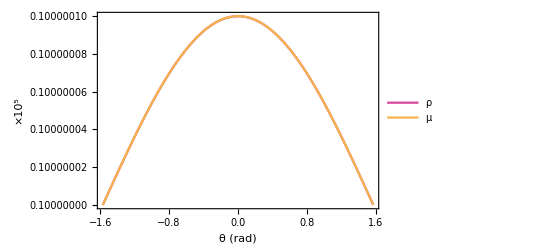
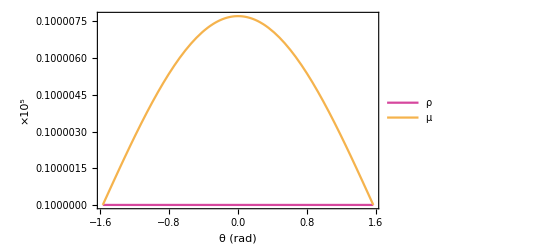
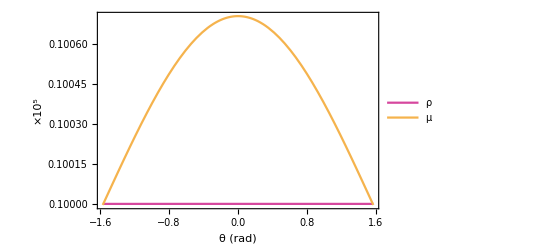
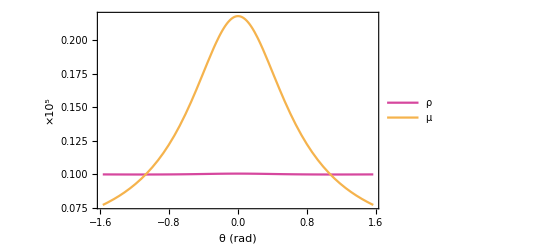
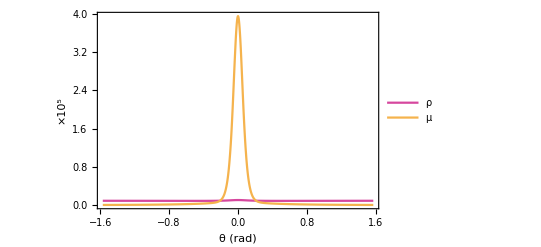
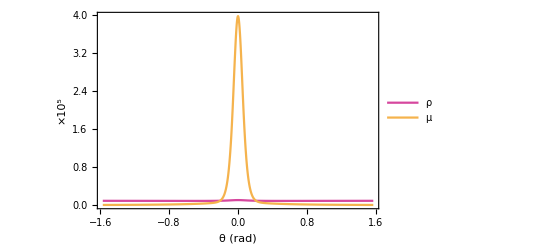
{-Graphics- t:0,-Graphics- t:60,-Graphics- t:120,-Graphics- t:180,-Graphics- t:240,-Graphics- t:300}

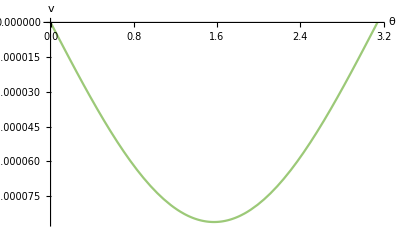
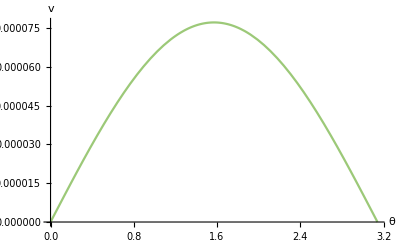
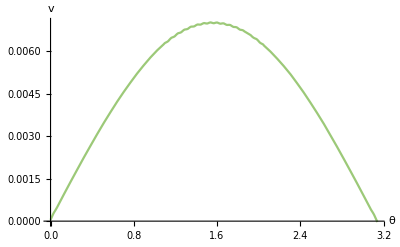
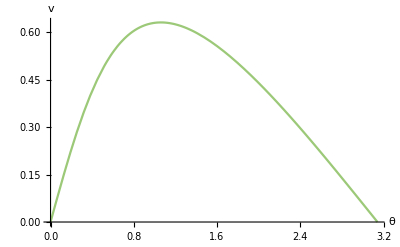
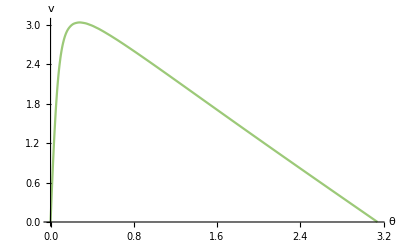
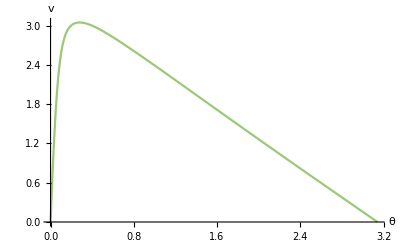
{-Graphics- t:0,-Graphics- t:60,-Graphics- t:120,-Graphics- t:180,-Graphics- t:240,-Graphics- t:300}

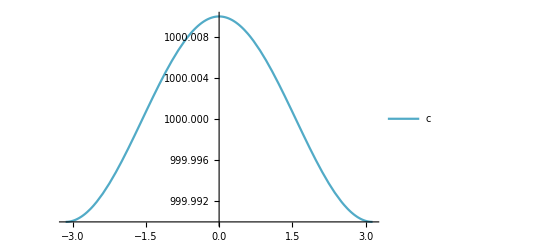
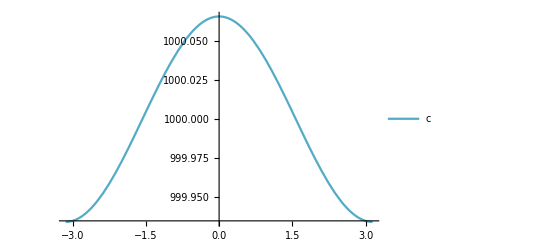
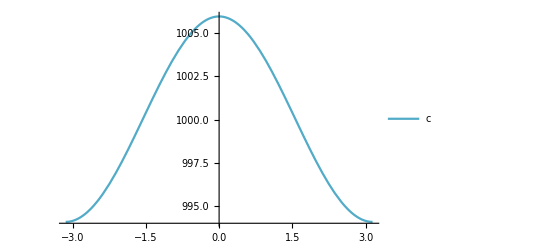
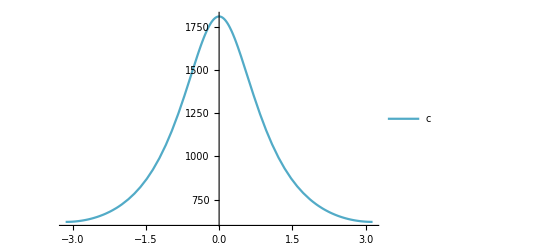
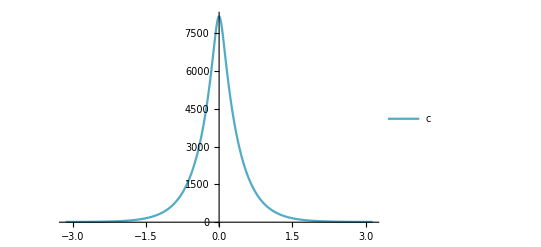
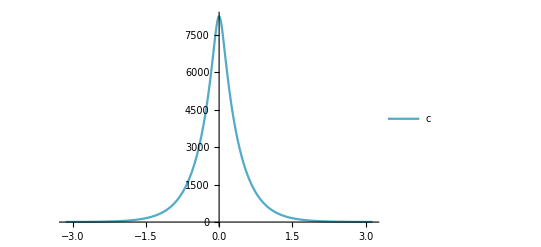
{-Graphics- t:0,-Graphics- t:60,-Graphics- t:120,-Graphics- t:180,-Graphics- t:240,-Graphics- t:300}

```mathematica
rhomuplot = plotSolrhoMu[0,Tend,Tend/5,solss]
velplot = plotSolVel[0,Tend,Tend/5,solss]
cplot = plotSolc[0,Tend,Tend/5,solss]
```

```mathematica
(* extract steady state to continue solution with perturbation*)
csol= c/.solss[[1]];
μsol = μ/.solss[[1]];
ρsol = ρ/.solss[[1]];
vsol = v/.solss[[1]];
```

```mathematica
css=Interpolation[Transpose[Append[{csol["Coordinates"][[1]]},csol["ValuesOnGrid"][[All,-1]]]],InterpolationOrder->csol["InterpolationOrder"][[1]],Method->csol["InterpolationMethod"],PeriodicInterpolation->True];
μss=Interpolation[Transpose[Append[{μsol["Coordinates"][[1]]},μsol["ValuesOnGrid"][[All,-1]]]],InterpolationOrder->μsol["InterpolationOrder"][[1]],Method->μsol["InterpolationMethod"],PeriodicInterpolation->True];
ρss=Interpolation[Transpose[Append[{ρsol["Coordinates"][[1]]},ρsol["ValuesOnGrid"][[All,-1]]]],InterpolationOrder->ρsol["InterpolationOrder"][[1]],Method->ρsol["InterpolationMethod"],PeriodicInterpolation->True];
vss=Interpolation[Transpose[Append[{vsol["Coordinates"][[1]]},vsol["ValuesOnGrid"][[All,-1]]]],InterpolationOrder->vsol["InterpolationOrder"][[1]],Method->vsol["InterpolationMethod"],PeriodicInterpolation->True];
(* see stack exchange post https://mathematica.stackexchange.com/questions/110377/extract-one-dimension-from-an-n-dimensional-interpolatingfunction?rq=1 *)
```

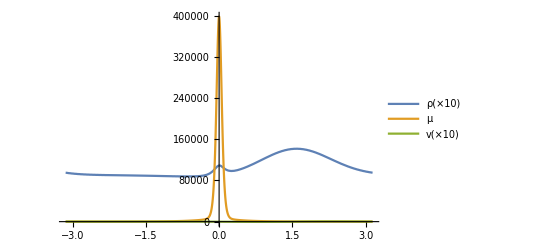

```mathematica
(* set and plot perturbation*)
Tplus = 20;
θp = Pi*4/8;
sp = 0.5;

(*apply perturbations, note here perturbation in mu is set to 0*)
μp[θ_,θpp_,spp_]:= 0*spp*μss[0]*(Exp[-(θ-θpp)^2] + Exp[-(θ-(θpp + 2Pi))^2]+ Exp[-(θ-(θpp - 2Pi))^2])
ρp[θ_,θpp_,spp_]:= spp*ρss[0]*(Exp[-(θ-θpp)^2] + Exp[-(θ-(θpp + 2Pi))^2]+ Exp[-(θ-(θpp - 2Pi))^2])
μpp0[θ_,θpp_,spp_] := μss[θ]+μp[θ,θpp,spp]
ρpp0[θ_,θpp_,spp_] := ρss[θ] +ρp[θ,θpp,spp]
vp[θ_,θpp_,spp_]= D[(-ζ*μp[θ,θpp,spp]-α*ρp[θ,θpp,spp] + (β/R^2)*D[ρp[θ,θpp,spp], θ,θ]), θ]/ξ /R //.ssvars;
vpp0[θ_,θpp_,spp_]=vss[θ] + vp[θ,θpp,spp];
(*use = instead of := to not delay evaluation of derivative*)
Plot[{ρpp0[θ,θp,sp]*10,μpp0[θ,θp,sp],vpp0[θ,θp,sp]*10},{θ,-Pi,Pi},PlotLegends->{"ρ(×10)","μ","v(×10)"},PlotRange->All] (* note different scales of steady state + perturbation in ρ and v!*)
```

```mathematica
(* now solve the PDE again with initial conditions at steady state, plus a perturbation *)
pdeSolvePerturb[rdvariables_,θpp_,spp_] :=Module[{sol},
sol = NDSolve[{
D[ρ[θ, t], t]+(1/R)*D[(ρ[θ, t] *v[θ, t]), θ]==kp*ρ[θ, t]^n/(K^2+ρ[θ, t]^n)-kd*μ[θ, t]*ρ[θ, t],
D[(-ζ*μ[θ, t] -α*ρ[θ, t] + (β/R^2)*D[ρ[θ, t], θ,θ]), θ] ==ξ *R *v[θ, t],
D[c[θ, t], t]== (Dc/R^2)* D[c[θ, t], θ,θ]-kon*ρ[θ, t]*c[θ, t]+koff*μ[θ, t],
D[μ[θ, t], t]+(1/R)* D[(μ[θ, t]*v[θ, t]), θ]== kon*ρ[θ, t]*c[θ, t]-koff*μ[θ, t] + (Dμ/R^2)*D[μ[θ,t], θ,θ],

c[θ, 0]== css[θ],
μ[θ, 0] ==μpp0[θ,θpp,spp],
ρ[θ,0]==ρpp0[θ,θpp,spp],
v[θ,0] == vpp0[θ,θpp,spp],
(*(∂_t c[θ, t]/.t->0)== koff*μp[θ,θpp,spp],
(∂_t ρ[θ, t]/.t->0)==-(1/R)*∂_θ (ρss[θ] *vp[θ ,θpp,spp])-kd*μp[θ,θpp,spp]*ρss[θ],
(∂_t μ[θ, t]/.t->0)==-(1/R)* ∂_θ (μp[θ ,θpp,spp]*vp[θ ,θpp,spp]+μss[θ]*vp[θ ,θpp,spp]+μp[θ ,θpp,spp]*vss[θ])-koff*μp[θ ,θpp,spp] + (Dμ/R^2)*∂_(θ,θ) μp[θ ,θpp,spp],*)

μ[-Pi, t]==μ[Pi, t],
c[-Pi, t]==c[Pi, t],
ρ[-Pi, t]==ρ[Pi, t],
v[-Pi,t]==v[Pi,t]
}//.rdvariables,{μ, c, ρ, v},{θ,-Pi,Pi},{t, 0,Tplus}, MaxStepFraction->1/200,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MaxPoints"->400}},AccuracyGoal->1,PrecisionGoal->2]; Return[sol]]
(*or: Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MaxPoints"->200}}*)
```

```mathematica
solpp = pdeSolvePerturb[ssvars,θp,sp]
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::mxsst: Using maximum number of grid points 400 allowed by the MaxPoints or MinStepSize options for independent variable θ.

{{μ→InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 20.}}, <>],c→InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 20.}}, <>],ρ→InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 20.}}, <>],v→InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 20.}}, <>]}}

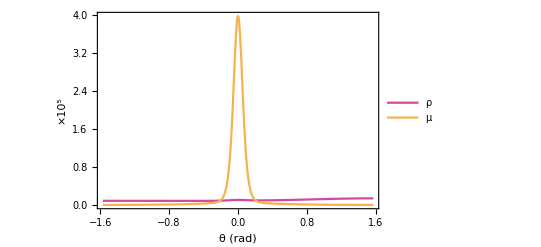
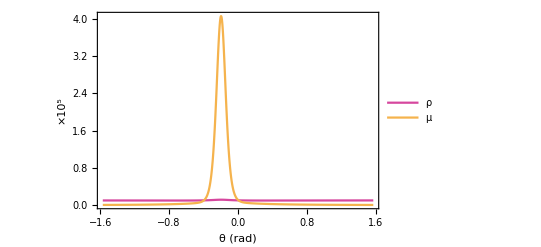
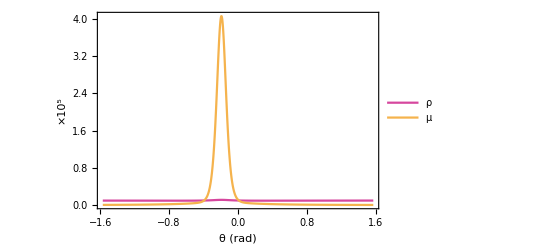
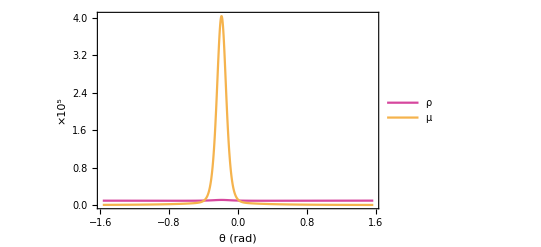
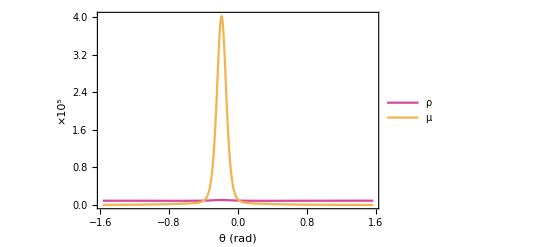
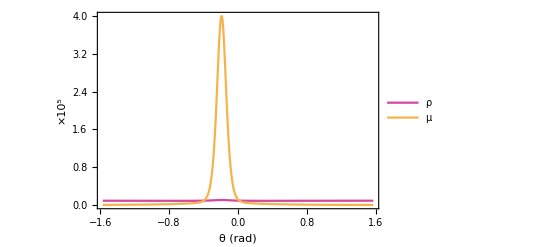
{-Graphics- t:0,-Graphics- t:4,-Graphics- t:8,-Graphics- t:12,-Graphics- t:16,-Graphics- t:20}

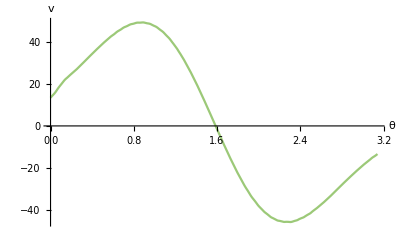
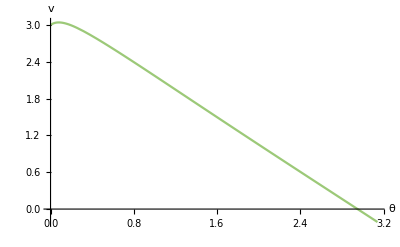
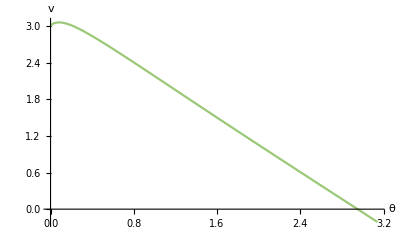
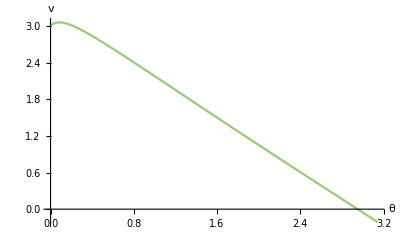
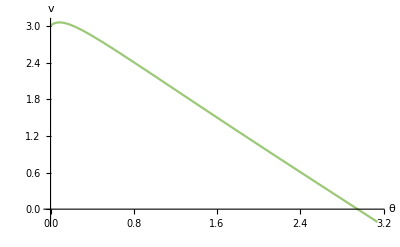
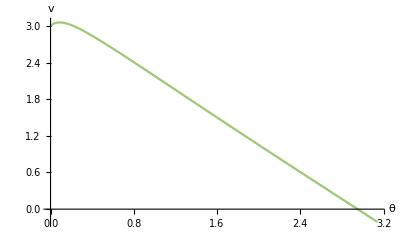
{-Graphics- t:0,-Graphics- t:4,-Graphics- t:8,-Graphics- t:12,-Graphics- t:16,-Graphics- t:20}

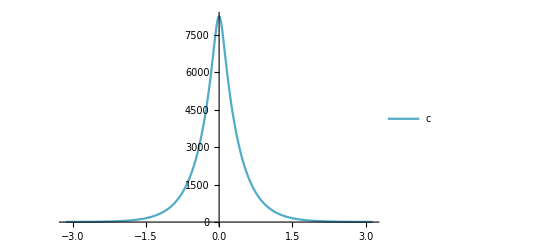
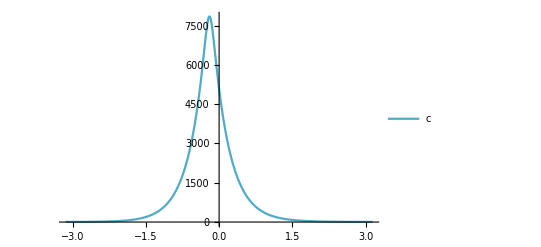
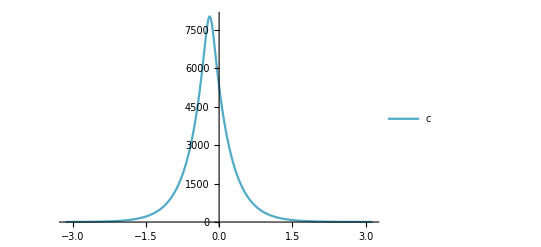
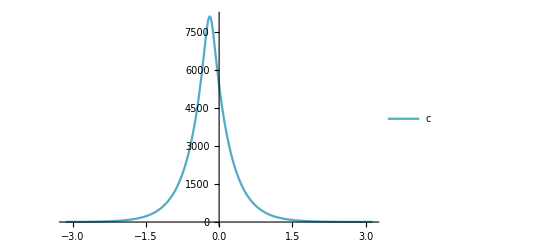
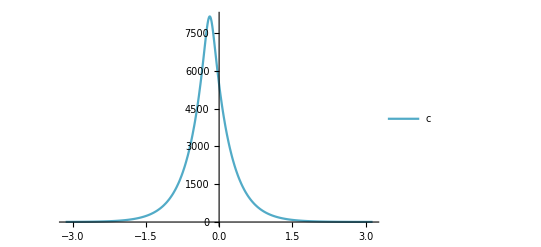
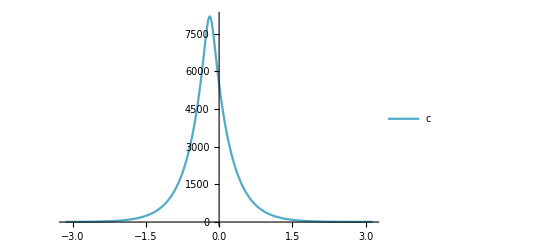
{-Graphics- t:0,-Graphics- t:4,-Graphics- t:8,-Graphics- t:12,-Graphics- t:16,-Graphics- t:20}

```mathematica
rhomuplotpp = plotSolrhoMu[0,Tplus,Tplus/5,solpp]
velplotpp = plotSolVel[0,Tplus,Tplus/5,solpp]
cplotpp = plotSolc[0,Tplus,Tplus/5,solpp]
```

```mathematica
θf = θ/.Last[FindMaximum[{Flatten[μ/.solpp[[1]] ][θ,Tplus/1]},{{θ,0}}]]
```

-0.191259

```mathematica
θfinal[θpp_,spp_] := θ/.Last[FindMaximum[{Flatten[μ/.pdeSolvePerturb[ssvars,θpp,spp][[1]] ][θ,Tplus]},{{θ,0}}]]
```

```mathematica
(* solve for a given perturbation strength and a range of angles*)
sp=0.5;
θpList = Pi*Range[1/8,7/8,1/16];
θfListAngles = θfinal[#,sp]&/@θpList; (*this step will take a long time *)
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::mxsst: Using maximum number of grid points 400 allowed by the MaxPoints or MinStepSize options for independent variable θ.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::mxsst: Using maximum number of grid points 400 allowed by the MaxPoints or MinStepSize options for independent variable θ.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

General::stop: Further output of NDSolve::pdord will be suppressed during this calculation.

NDSolve::mxsst: Using maximum number of grid points 400 allowed by the MaxPoints or MinStepSize options for independent variable θ.

General::stop: Further output of NDSolve::mxsst will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

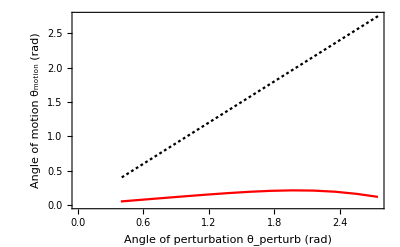

```mathematica
muangleplot = ListLinePlot[{Transpose[{Pi-θpList,Pi-θpList}],Transpose[{Pi-θpList,-θfListAngles}]},PlotStyle->{{Dashing[Tiny],RGBColor[0,0,0]},{RGBColor[1,0,0]}},Axes->False,Frame->{{True,False},{True,None}},FrameLabel->{{"Angle of motion θ_motion (rad)",None},{"Angle of perturbation θ_perturb (rad)",None}},BaseStyle->{FontSize->14}](*plot angles wrt to direction of motion*)
```

```mathematica
(* solve for a given perturbation angle and a range of strengths*)
θp = Pi*1/4;
spList = Range[0.01,0.5,0.05];
θfListStrengths = θfinal[θp,#]&/@spList; (*this step will take a long time *)
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::mxsst: Using maximum number of grid points 400 allowed by the MaxPoints or MinStepSize options for independent variable θ.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::mxsst: Using maximum number of grid points 400 allowed by the MaxPoints or MinStepSize options for independent variable θ.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

General::stop: Further output of NDSolve::pdord will be suppressed during this calculation.

NDSolve::mxsst: Using maximum number of grid points 400 allowed by the MaxPoints or MinStepSize options for independent variable θ.

General::stop: Further output of NDSolve::mxsst will be suppressed during this calculation.

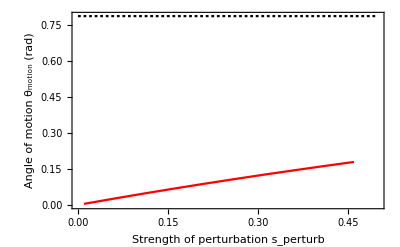

```mathematica
musplot = ListPlot[{Transpose[{{0,0.5},{θp,θp}}],Transpose[{spList,-θfListStrengths}]},PlotStyle->{{Dashing[Tiny],RGBColor[0,0,0]},RGBColor[1,0,0]},Joined->True,Axes->False,Frame->{{True,False},{True,None}},FrameLabel->{{"Angle of motion θ_motion (rad)",None},{"Strength of perturbation s_perturb",None}},PlotRange->All,BaseStyle->{FontSize->14}]
```